```mathematica
(*ep=6.7;β=0.75;γ=0.086;*)
xmin=-50;xmax=50;maxtime=150;δ=0; d1=1;d2=1; 
τ=131.5;α=0.081;γt=1.62;
(*eqn=FindRoot[v-v^3/3-(v+β)/γ,{v,-1}];
{v0,w0}={v,(v+β)/γ}/.eqn;*)
If[γt <3α^2/(2(1-2α)),"Satisfies first standing pulse hypothesis", "Does not satisfy first standing pulse hypothesis"]
If[τ<γt^2,"Satisfies Stability hypothesis for standing pulse", "Does not satisfy Stability hypothesis for standing pulse"]
d2=1.5;d1=1;
ρ0[x_]=d2*d1^(3/2)/(d1+x^2)^(3/2);
ρ[x_]=Which[ρ0[x]>0.5,1,True,0];
f[v_]=v-v^3/3;
f[v_]=v(1-v)(v-α);
```

Does not satisfy first standing pulse hypothesis

Does not satisfy Stability hypothesis for standing pulse

```mathematica
{V1,W1}=NDSolveValue[{D[u[t, x], t] == d1 D[u[t, x], x, x]+f[u[t,x]] - w[t,x]+(1+α-3u[t,x])ρ[x]^2/2, τ D[w[t, x], t] == d2 D[w[t, x], x, x] + (u[t, x] - γt w[t, x]), 
u[0, x] == 0, 
w[0, x] ==0,
u[t, xmin] == 0, 
u[t, xmax] == 0, w[t, xmin] == 0,w[t, xmax] == 0}, {u, w}, {t, 0, maxtime}, {x, xmin, xmax}]
{V2,W2}=NDSolveValue[{D[u[t, x], t] == d1 D[u[t, x], x, x]+f[u[t,x]] - w[t,x]+(1+α-3u[t,x])ρ[x]^2/2, τ D[w[t, x], t] == d2 D[w[t, x], x, x] + (u[t, x] - γt w[t, x]), 
u[0, x] == V1[maxtime,x], 
w[0, x] ==W1[maxtime,x],
u[t, xmin] == 0, 
u[t, xmax] == 0, w[t, xmin] == 0,w[t, xmax] == 0}, {u, w}, {t, 0, maxtime}, {x, xmin, xmax}]
{V3,W3}=NDSolveValue[{D[u[t, x], t] == d1 D[u[t, x], x, x]+f[u[t,x]] - w[t,x]+(1+α-3u[t,x])ρ[x]^2/2, τ D[w[t, x], t] == d2 D[w[t, x], x, x] + (u[t, x] - γt w[t, x]), 
u[0, x] == V2[maxtime,x]+Which[Abs[x+45] <=1,3,True, 0], 
w[0, x] ==V2[maxtime,x],
u[t, xmin] == 0, 
u[t, xmax] == 0, w[t, xmin] == 0,w[t, xmax] == 0}, {u, w}, {t, 0, maxtime}, {x, xmin, xmax}]
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

NDSolveValue::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

{InterpolatingFunction[{{0., 150.}, {-50., 50.}}, <>],InterpolatingFunction[{{0., 150.}, {-50., 50.}}, <>]}

NDSolveValue::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

{InterpolatingFunction[{{0., 150.}, {-50., 50.}}, <>],InterpolatingFunction[{{0., 150.}, {-50., 50.}}, <>]}

```mathematica
Plot3D[V3[t,x], {t, 0, maxtime}, {x, xmin, xmax},PlotRange->{-2,2},AxesLabel->{"time","space"},Mesh->All]
```

-Graphics3D-

```mathematica
Animate[Plot[{V3[t,x],W3[t,x],ρ[x]^2/2},{x,xmin,xmax},PlotRange->{{xmin,xmax},{-2,2}}],{t,0,maxtime},AnimationRunning->False,AnimationRepetitions->1]
```

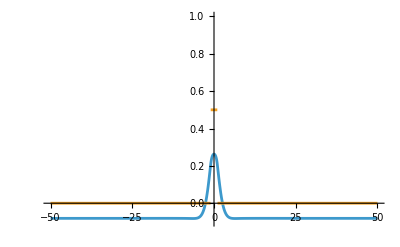

```mathematica
Plot[{-α+2(1+α)V2[maxtime,x]-3V2[maxtime,x]^2,ρ[x]^2/2},{x,xmin,xmax},PlotRange->{-0.1,1}]
```